### My emission channel:

```mathematica
K0[ajp_,aj_,Γ_]:=KroneckerDelta[ajp,0] KroneckerDelta[aj,0] + Sqrt[1-Γ](KroneckerDelta[aj,ajp] -KroneckerDelta[ajp,0] KroneckerDelta[aj,0])
Ki[ajp_,aj_,i_,Γ_]:=Sqrt[Γ] KroneckerDelta[ajp,i-1] KroneckerDelta[aj,i]
SigmaTau[a1_,b1_,b2_,σ_]:= KroneckerDelta[σ,1]KroneckerDelta[a1,b1]+(1-KroneckerDelta[σ,1])KroneckerDelta[a1,b2]
wg[c_,τ_,q_]:= KroneckerDelta[c,τ]/(q^2-1) -(1- KroneckerDelta[c,τ])/(q(q^2-1))
```

### If I change Gamma to 1-exp(-Gamma):

```mathematica
K0Exp[ajp_,aj_,Γ_]:=KroneckerDelta[ajp,0] KroneckerDelta[aj,0] + (Exp[-Γ/2])(KroneckerDelta[aj,ajp] -KroneckerDelta[ajp,0] KroneckerDelta[aj,0])
KiExp[ajp_,aj_,i_,Γ_]:=Sqrt[(1-Exp[-Γ])] KroneckerDelta[ajp,i-1] KroneckerDelta[aj,i]
SigmaTau[a1_,b1_,b2_,σ_]:= KroneckerDelta[σ,1]KroneckerDelta[a1,b1]+(1-KroneckerDelta[σ,1])KroneckerDelta[a1,b2]
wg[c_,τ_,q_]:= KroneckerDelta[c,τ]/(q^2-1) -(1- KroneckerDelta[c,τ])/(q(q^2-1))
```

### Proceed to building bigger things...

```mathematica
K0K0dagExp[ajp_,aj_,bjp_,bj_,Γ_]:=K0Exp[ajp,aj,Γ]*K0Exp[bj,bjp,Γ]
KiKidagExp[ajp_,aj_,bjp_,bj_,i_,Γ_]:=KiExp[ajp,aj,i,Γ]*KiExp[bjp,bj,i,Γ]
```

```mathematica
wd[σ_,τ_,q_,Γ_,p_]:=Sum[(K0K0dag[a0p,a0,b0p,b0,Γ]+Sum[KiKidag[a0p,a0,b0p,b0,i,Γ],{i,0,q-1}])*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*(K0K0dag[a1p,a1,b1p,b1,Γ]+Sum[KiKidag[a1p,a1,b1p,b1,i,Γ],{i,0,q-1}])*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ]((1-p)^2 + p^2 *KroneckerDelta[b0p,a1p]KroneckerDelta[b0p,a0p]KroneckerDelta[b1p,a0p]KroneckerDelta[b1p,a1p]),{a1,0,q-1},{a1p,0,q-1},{b1,0,q-1},{b1p,0,q-1},{a0,0,q-1},{a0p,0,q-1},{b0,0,q-1},{b0p,0,q-1},Assumptions->{p>0,q>0,Element[q,Integers]}]
w3a[a_,b_,c_,q_,Γ_,p_]:=wd[a,1,q,Γ,p] wd[b,1,q,Γ,p]wg[c,1,q^2]+wd[a,-1,q,Γ,p] wd[b,-1,q,Γ,p]wg[c,-1,q^2]
w3b[a_,b_,c_,q_,Γ_,p_]:=wd[1,a,q,Γ,p] wd[1,b,q,Γ,p]wg[1,c,q^2]+wd[-1,a,q,Γ,p] wd[-1,b,q,Γ,p]wg[-1,c,q^2]
```

```mathematica
Simplify[w3a[1,-1,1,q,Γ,p]-w3b[1,-1,1,q,Γ,p]]
```

1/15 Γ (Γ (10-2 Γ+Γ^2)-4 p Γ (10-2 Γ+Γ^2)+3 p^4 (5+4 Γ+Γ^2+2 Γ^3)-2 p^3 (10+23 Γ-4 Γ^2+7 Γ^3)+p^2 (10+63 Γ-12 Γ^2+11 Γ^3))

```mathematica
Simplify[Series[wd[1,1,2,Γ,p],{Γ,0,1}]]
Simplify[Series[wd[-1,1,2,Γ,p],{Γ,0,1}]]
Simplify[Series[wd[1,-1,2,Γ,p],{Γ,0,1}]]
Simplify[Series[wd[-1,-1,2,Γ,p],{Γ,0,1}]]
```

(4-8 p+6 p^2)+O[Γ]^2

(2-4 p+4 p^2)+O[Γ]^2

(2-4 p+4 p^2)-2 p^2 Γ+O[Γ]^2

(4-8 p+6 p^2)+(-4+8 p-6 p^2) Γ+O[Γ]^2

```mathematica
wdExp[σ_,τ_,q_,Γ_,p_]:=Sum[(K0K0dagExp[a0p,a0,b0p,b0,Γ]+Sum[KiKidagExp[a0p,a0,b0p,b0,i,Γ],{i,0,q-1}])*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*(K0K0dagExp[a1p,a1,b1p,b1,Γ]+Sum[KiKidagExp[a1p,a1,b1p,b1,i,Γ],{i,0,q-1}])*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ]((1-p)^2 + p^2 *KroneckerDelta[b0p,a1p]KroneckerDelta[b0p,a0p]KroneckerDelta[b1p,a0p]KroneckerDelta[b1p,a1p]),{a1,0,q-1},{a1p,0,q-1},{b1,0,q-1},{b1p,0,q-1},{a0,0,q-1},{a0p,0,q-1},{b0,0,q-1},{b0p,0,q-1},Assumptions->{p>0,q>0,Element[q,Integers]}]
```

```mathematica
w3aExp[a_,b_,c_,q_,Γ_,p_]:=wdExp[a,1,q,Γ,p] wdExp[b,1,q,Γ,p]wg[c,1,q^2]+wdExp[a,-1,q,Γ,p] wdExp[b,-1,q,Γ,p]wg[c,-1,q^2]
w3bExp[a_,b_,c_,q_,Γ_,p_]:=wdExp[1,a,q,Γ,p] wdExp[1,b,q,Γ,p]wg[1,c,q^2]+wdExp[-1,a,q,Γ,p] wdExp[-1,b,q,Γ,p]wg[-1,c,q^2]
```

```mathematica
Simplify[Series[wdExp[1,1,2,Γ,p],{Γ,0,1}]]
Simplify[Series[wdExp[-1,1,2,Γ,p],{Γ,0,1}]]
Simplify[Series[wdExp[1,-1,2,Γ,p],{Γ,0,1}]]
Simplify[Series[wdExp[-1,-1,2,Γ,p],{Γ,0,1}]]
```

(4-8 p+6 p^2)+O[Γ]^2

(2-4 p+4 p^2)+O[Γ]^2

(2-4 p+4 p^2)-2 p^2 Γ+O[Γ]^2

(4-8 p+6 p^2)+(-4+8 p-6 p^2) Γ+O[Γ]^2

```mathematica
wdtest[σ_,τ_,q_,Γ_,p_]:=
Which [σ==1&&τ==1,(1/2*q(1+q)+Γ^2) 2p^2-2q^2  p + q^2,
σ==-1&&τ==-1,(1-p)^2(1+2(q-1)(1-Γ)+(q-1)(q-2)(1-Γ)^2+(q-1)((1-Γ)^2+Γ^2) )+p^2(1+(q-1)((1-Γ)^2+Γ^2)),
σ==-1 &&τ==1,(1-2p+2p^2)(2Γ^2+q),
σ==1&&τ==-1, q-2q p + p^2(2q-2(q-1)(Γ-Γ^2))
]
w3test[a_,b_,c_,q_,Γ_,p_]:=wdtest[a,1,q,Γ,p] wdtest[b,1,q,Γ,p]wg[c,1,q^2]+wdtest[a,-1,q,Γ,p] wdtest[b,-1,q,Γ,p]wg[c,-1,q^2]
```

```mathematica
testFun[σ_,τ_,p_,q_,Γ_]:= Sum[K0K0dag[a0p,a0,b0p,b0,Γ]*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*Sum[KiKidag[a1p,a1,b1p,b1,i,Γ],{i,0,q-1}]*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ],{a1,0,q-1},{a1p,0,q-1},{b1,0,q-1},{b1p,0,q-1},{a0,0,q-1},{a0p,0,q-1},{b0,0,q-1},{b0p,0,q-1},Assumptions->{q>0,Element[q,Integers]}]
(*testFun[σ_,τ_,p_,q_,Γ_]:= Sum[K0K0dag[a0p,a0,b0p,b0,Γ]*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*K0K0dag[a1p,a1,b1p,b1,Γ]*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ],{a1,0,q-1},{a1p,0,q-1},{b1,0,q-1},{b1p,0,q-1},{a0,0,q-1},{a0p,0,q-1},{b0,0,q-1},{b0p,0,q-1},Assumptions->{q>0,Element[q,Integers]}]*)
```

```mathematica
K0[ajp_,aj_,Γ_]:=KroneckerDelta[ajp,0] KroneckerDelta[aj,0] + Sqrt[1-Γ](KroneckerDelta[aj,ajp] -KroneckerDelta[ajp,0] KroneckerDelta[aj,0])
Ki[ajp_,aj_,i_,Γ_]:=Sqrt[Γ] KroneckerDelta[ajp,i-1] KroneckerDelta[aj,i]
```

```mathematica
testFun[-1,-1,p,3,Γ]
testFun[-1,1,p,3,Γ]
testFun[1,-1,p,3,Γ]
testFun[1,1,p,3,Γ]
```

0

Γ+(1-Γ) Γ

2 (1-Γ) Γ

2 Γ+4 (1-Γ) Γ

```mathematica
Series[wd[-1,-1,2,Γ,p],{Γ,0,2}]
```

2 (2-4 p+3 p^2)-2 (2-4 p+3 p^2) Γ+(4-8 p+7 p^2) Γ^2+O[Γ]^3

```mathematica
Simplify[wd[-1,-1,3,Γ,p]]
Simplify[wd[-1,1,3,Γ,p]]
Simplify[wd[1,-1,3,Γ,p]]
FullSimplify[wd[1,1,3,Γ,p]]
```

9-12 Γ+6 Γ^2-6 p (3-4 Γ+2 Γ^2)+2 p^2 (6-8 Γ+5 Γ^2)

(1-2 p+2 p^2) (3+2 Γ^2)

3-6 p+p^2 (6-4 Γ+4 Γ^2)

9+2 p (-9+p (6+Γ^2))

```mathematica
Simplify[(1-p)^2(1+2(q-1)(1-Γ)+(1-Γ)^2(q-1)^2 + 2(q-1)Γ +2(q-1)^2Γ(1-Γ)+(q-1)^2 Γ^2)+p^2(1+(q-1)(1-Γ)^2+ Γ^2(q-1) +  2Γ)]
```

q^2-2 p q^2+p^2 (q^2-2 (-2+Γ) Γ+q (1-2 Γ+2 Γ^2))

```mathematica
Simplify[4-8 p+p^2 (4-2 (-2+Γ) Γ+2 (1-2 Γ+2 Γ^2))]
```

4-8 p+2 p^2 (3+Γ^2)

```mathematica
Simplify[wdtest[1,1,3,Γ,p]]
Simplify[wdtest[1,-1,3,Γ,p]]
Simplify[wdtest[-1,1,3,Γ,p]]
FullSimplify[wdtest[-1,-1,3,Γ,p]]
```

9-18 p+2 p^2 (6+Γ^2)

3-6 p+p^2 (6-4 Γ+4 Γ^2)

(1-2 p+2 p^2) (3+2 Γ^2)

9+6 (-2+Γ) Γ-6 p (3+2 (-2+Γ) Γ)+2 p^2 (6+Γ (-8+5 Γ))

```mathematica
Collect[Simplify[wdtest[1,1,q,Γ,p]],q]
Collect[Simplify[wdtest[1,-1,q,Γ,p]],q]
Collect[Simplify[wdtest[-1,1,q,Γ,p]],q]
Collect[Simplify[wdtest[-1,-1,q,Γ,p]],q]
```

p^2 q+(1-2 p+p^2) q^2+2 p^2 Γ^2

2 p^2 (1-Γ) Γ+q (1-2 p+2 p^2+2 p^2 (-1+Γ) Γ)

(1-2 p+2 p^2) q+2 (1-2 p+2 p^2) Γ^2

(-1+p)^2 q^2 (-1+Γ)^2+2 p^2 Γ-2 p^2 Γ^2+q (-(-1+p)^2 (-2+Γ) Γ+p^2 (1-2 Γ+2 Γ^2))

```mathematica
testFun[-1,-1,p,4,Γ]
testFun[1,-1,p,4,Γ]
testFun[1,1,p,4,Γ]
```

0

3 (1-Γ) Γ

3 Γ+9 (1-Γ) Γ

```mathematica
w110/.{Γ->0,q->2}
```

-1/60 (4 (1-p)^2+2 p^2)^2+4/15 (1-2 p+2 p^2)^2

```mathematica
w000=w3test[1,1,1,q,Γ,p];
w001=w3test[1,1,-1,q,Γ,p];
w010=w3test[1,-1,1,q,Γ,p];
w100=w3test[-1,1,1,q,Γ,p];
w101=w3test[-1,1,-1,q,Γ,p];
w011=w3test[1,-1,-1,q,Γ,p];
w110=w3test[-1,-1,1,q,Γ,p];
w111=w3test[-1,-1,-1,q,Γ,p];
```

## Thermodynamic limit

```mathematica
n=100;
minFA1=Min[-(2n+1)Log[w110]-Log[w010]-Log[w100]-(2n+1)Log[w000],-n Log[w001]-(n+1)Log[w111]-(n+2)(Log[w010]+Log[w100])+2(n+1)Log[w000] -(2n+1)Log[w000]];
minFAB =Min[-(2n+2)(Log[w110]+Log[w111]+Log[w010]+Log[w100]-2Log[w000]),-(4n+4)(Log[w110]+2Log[w000])];
Fempty1=-(4n+4)Log[w000];
minFA2=Min[-(2n+1)Log[w110]-Log[w010]-Log[w100]-(2n+1)Log[w000],-(n+1) Log[w001]-(n+2)(Log[w010]+Log[w100])-n Log[w111]-(2n+1)Log[w000] ];
minFA3=Min[-2n Log[w110]-Log[w010]-Log[w100]-2n Log[w000],-n Log[w001]-n Log[w111]-(n+1)(Log[w010]+Log[w100])-2n Log[w000] ];
minFAB3 =Min[-(2n+1)(Log[w110]+Log[w111]+Log[w010]+Log[w100]),-(4n+2)(Log[w110]+2Log[w000])];
Fempty3=-(4n+2)Log[w000];
```

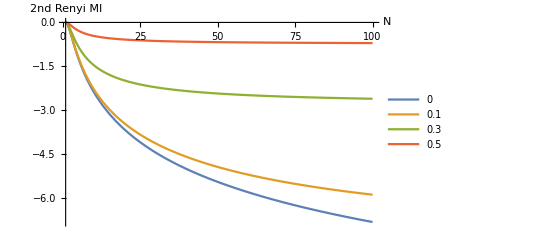

```mathematica
renyiMI2N = Plot[{-2Log[w100*w010/(w110*w000)]/.{q->2,p->0,Γ->(1/n)},-2Log[w100*w010/(w110*w000)]/.{q->2,p->.1,Γ->(1/n)},
-2Log[w100*w010/(w110*w000)]/.{q->2,p->.3,Γ->(1/n)},
-2Log[w100*w010/(w110*w000)]/.{q->2,p->.5,Γ->(1/n)}},{n,1,100},AxesLabel->{"N","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->{0,0.1,0.3,0.5}]
Export["/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2N.png",Rasterize[renyiMI2N,ImageResolution->150]];
```

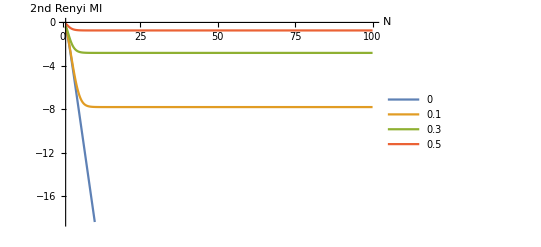

```mathematica
Plot[{-2Log[w100*w010/(w110*w000)]/.{q->2,p->0,Γ->(Exp[-n])},-2Log[w100*w010/(w110*w000)]/.{q->2,p->.1,Γ->(Exp[-n])},
-2Log[w100*w010/(w110*w000)]/.{q->2,p->.3,Γ->(Exp[-n])},
-2Log[w100*w010/(w110*w000)]/.{q->2,p->.5,Γ->(Exp[-n])}},{n,1,100},AxesLabel->{"N","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->{0,0.1,0.3,0.5}]
```

```mathematica
Clear[p,Γ,q]
(w000)/.{q->2,p->0,Γ->0}
```

1

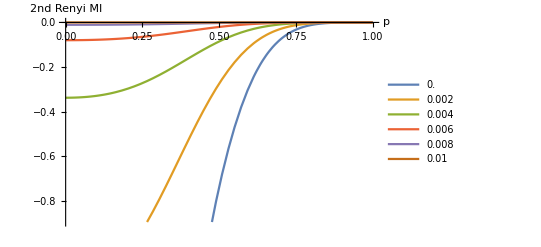

/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2_area.png

```mathematica
renyiMI2 = Plot[Evaluate[Table[-2Log[w100*w010/(w110* w000)]/.{q->2,Γ->.01*g},{g,0,100,20}]],{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.0001*g,{g,0,100,20}],Spacings->0.15],PlotRange->Automatic]
Export["/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2_area.png",Rasterize[renyiMI2,ImageResolution->150]]
```

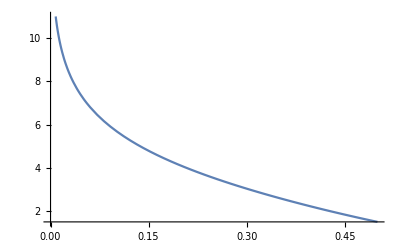

1

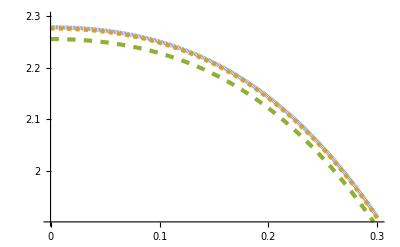

/Users/cathy/Google Drive/Random circuits/Pics/volumePref.png

```mathematica
Plot[-Log[(w001/w111)]/.{q->2,Γ->0},{p,0,0.5}]
Clear[q]
Simplify[w111*w000/.{Γ->0,p->0}]
volc=Plot[{Max[(-2Log[(w101*w010)]+2Log[w000*w111]-2Log[2])/.{q->2,Γ->0},0],
Max[(-2Log[(w101*w010)]+2Log[w000*w111]-2Log[2])/.{q->2,Γ->0.001},0],
Max[(-2Log[(w101*w010)]+2Log[w000*w111]-2Log[2])/.{q->2,Γ->0.01},0]},{p,0,0.3},
PlotStyle->dashThick,
PlotLegends->LineLegend[Automatic,{"0","10^-3","10^-2"},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2.5]],
AxesLabel->{MaTeX["p",Magnification->2.5],MaTeX["v_2(p,\\Gamma)",Magnification->2.5]},
Ticks->{{0,0.1,0.2,0.3},{2,2.1,2.2,2.3}},
PlotRange->{{0,0.3},{1.9,2.3}},LabelStyle->{FontSize->22}]
Export["/Users/cathy/Google Drive/Random circuits/Pics/volumePref.png",Rasterize[volc,ImageResolution->4]]
```

```mathematica
Simplify[2Log[w000*w111/(w101*w010)]-2Log[2]]
```

-Log[4]+2 Log[((-((q-2 p q+2 p^2 (q+(-1+q) (-1+Γ) Γ))^2)/q^2+(q^2-2 p q^2+p^2 (q+q^2+2 Γ^2))^2) (-((1-2 p+2 p^2)^2 (q+2 Γ^2)^2)/q^2+((-1+p)^2 q (q (-1+Γ)^2-(-2+Γ) Γ)+p^2 (1+(-1+q) (1-2 Γ+2 Γ^2)))^2))/(((1-2 p+2 p^2) (q+2 Γ^2) (q^2-2 p q^2+p^2 (q+q^2+2 Γ^2))-1/q^2(q-2 p q-2 p^2 (-1+Γ) Γ+2 p^2 q (1-Γ+Γ^2)) (q (q (-1+Γ)^2-(-2+Γ) Γ)-2 p q (q (-1+Γ)^2-(-2+Γ) Γ)+p^2 (q^2 (-1+Γ)^2-2 (-1+Γ) Γ+q (1+Γ^2)))) (-((1-2 p+2 p^2) (q+2 Γ^2) (q^2-2 p q^2+p^2 (q+q^2+2 Γ^2)))/q^2+(q-2 p q+2 p^2 (q+(-1+q) (-1+Γ) Γ)) ((-1+p)^2 q (q (-1+Γ)^2-(-2+Γ) Γ)+p^2 (1+(-1+q) (1-2 Γ+2 Γ^2)))))]

```mathematica
Plot[{-2Log[w010 *w011/w110]/.{q->2,Γ->0.},-2Log[w010 *w011/w110]/.{q->2,Γ->0.001},-2Log[w010 *w011/w110]/.{q->2,Γ->0.01}},{p,0,1}]
```

```mathematica
w001/.{p->0,Γ->0}
Simplify[w110/.{p->0,Γ->0}]
Simplify[w000/.{p->0,Γ->0}]
Simplify[w010/.{p->0,Γ->0}]
Simplify[w011/.{p->0,Γ->0}]
```

0

0

1

q/(1+q^2)

q/(1+q^2)

0

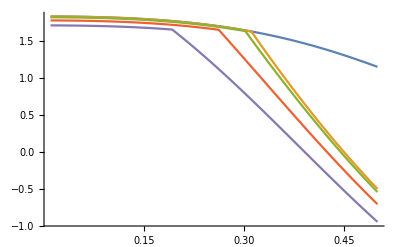

/Users/cathy/Google Drive/Random circuits/Pics/volumePref.png

```mathematica
w001/.{p->0,Γ->0}
volc=Plot[{Min[-Log[w101*w010/w111/w000]]/.{q->2,Γ->0},
Min[-Log[w110/w111/w000],-Log[w101*w010/w111/w000]]/.{q->2,Γ->0.001},
Min[-Log[w110/w111/w000],-Log[w101*w010/w111/w000]]/.{q->2,Γ->0.01},
Min[-Log[w110/w111/w000],-Log[w101*w010/w111/w000]]/.{q->2,Γ->0.046},
Min[-Log[w110/w111/w000],-Log[w101*w010/w111/w000]]/.{q->2,Γ->0.1}}
,{p,0.01,0.5}, PlotLegends->LineLegend[Automatic,{0,0.001,0.01,0.046,0.1},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2]],AxesLabel->{MaTeX["p",Magnification->2],MaTeX["c(p,\\Gamma)",Magnification->2]},LabelStyle->{FontSize->22}]
Export["/Users/cathy/Google Drive/Random circuits/Pics/volumePref.png",Rasterize[volc,ImageResolution->150]]
```

Fix the system size nTot,

```mathematica
Shalf/.{p->0.1,Γ->0.1,q->2}
```

Log[1/(√π (15+h)!)2^(2 h) (-14+h) (-13+h) (-12+h) (-11+h) (-10+h) (-9+h) (-8+h) (-7+h) (-6+h) (-5+h) (-4+h) (-3+h) (-2+h) (-1+h) h (1/2 (-1+2 h))!]

```mathematica
Simplify[Sum[Binomial[h,y]*Binomial[h,(y-nTot/2)],{y,nTot/2,h}]]
```

1/(√π (50+h)!)4^h (-49+h) (-48+h) (-47+h) (-46+h) (-45+h) (-44+h) (-43+h) (-42+h) (-41+h) (-40+h) (-39+h) (-38+h) (-37+h) (-36+h) (-35+h) (-34+h) (-33+h) (-32+h) (-31+h) (-30+h) (-29+h) (-28+h) (-27+h) (-26+h) (-25+h) (-24+h) (-23+h) (-22+h) (-21+h) (-20+h) (-19+h) (-18+h) (-17+h) (-16+h) (-15+h) (-14+h) (-13+h) (-12+h) (-11+h) (-10+h) (-9+h) (-8+h) (-7+h) (-6+h) (-5+h) (-4+h) (-3+h) (-2+h) (-1+h) h (-1/2+h)!

```mathematica
nTot=50;
deltaE =((h+nTot)*(-Log[w100])+(h-nTot)*(-Log[w101]) +h*nTot/2*(-Log[w111/w000]))/2;
Shalf = Log[Sum[Binomial[h,y]*Binomial[h,(y-nTot)],{y,nTot,h}]];
Stot = Log[nTot  * Sum[Binomial[h,y]*Binomial[h,(y-2nTot)],{y,2nTot,h}]];
h*nTot/2*(-Log[w111/w000])/.{p->.1,h->2*nTot,Γ->0.001,q->2}
(h-nTot)*(-Log[w101])/.{p->0.1,h->2*nTot,Γ->0.01,q->2}
(h+nTot)*(-Log[w100])/.{p->0.1,h->2*nTot,Γ->0.01,q->2}
N[Shalf/.{h->nTot*2}]
Plot[-2Shalf+Stot/.{h->nTot,Γ->0.001,q->2},{p,0,1}]
Plot[deltaE-Shalf/.{h->nTot,Γ->0.0,q->2},{p,0,1}]
```

5.34254

66.643

197.374

109.734

```mathematica
45*6
```

270

```mathematica
Needs["MaTeX`"]
```

```mathematica
Dashingstuff={{AbsoluteDashing[0],AbsoluteThickness[3]},{AbsoluteDashing[3],AbsoluteThickness[3]},{AbsoluteDashing[0],AbsoluteThickness[3]},{AbsoluteDashing[3],AbsoluteThickness[3]}};
```

```mathematica
n=1000;
Solve[-n Log[w100]-n(n-1)/8 Log[w111]-(n t -n-n(n-1)/8) Log[w000]==-2t(Log[w010])-(n-t)(t-1)/2 Log[w111]-(t^2/2)Log[w000] ,t]/.{q->2,Γ->0.001,p->0.1}
```

(t→-6.86375
t→-189495.)

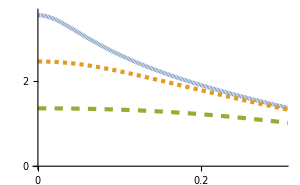

500

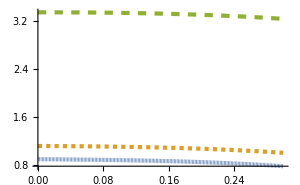

```mathematica
dashThick=Transpose[{Table[AbsoluteDashing[i],{i,0,11,3}],
Table[AbsoluteThickness[3],{i,1,4}]}];
SABsatTime = Plot[{Log[w110/w000]/Log[w111/w000]*Γ/.{Γ->0.001,q->2},Log[w110/w000]/Log[w111/w000]*Γ/.{Γ->0.01,q->2},Log[w110/w000]/Log[w111/w000]*Γ/.{Γ->0.1,q->2}},{p,0,0.5},PlotStyle-> dashThick,AxesLabel->{MaTeX["p",Magnification->2.5],MaTeX["\\Gamma \cdot t_{AB}^*(p,\\Gamma)",Magnification->2.5]},LabelStyle->{FontSize->24},PlotRange->{{0,0.3},{0,3.6}},Ticks->{{0,0.1,0.2,0.3,0.4,0.5},{0,1,2,3,4}},ImageSize->300]

n=500
SABsatTime2 = Plot[{Γ*(-(n-2)^2/2 Log[w111]+n^2/2*Log[w000]-(2n-4)*Log[w100]-2Log[w110] )/(n * (-Log[w111/w000]))/.{Γ->0.0001,q->2},Γ*(-(n-2)^2/2 Log[w111]+n^2/2*Log[w000]-(2n-4)*Log[w100]-2Log[w110] )/(n * (-Log[w111/w000]))/.{Γ->0.001,q->2},
Γ*(-(n-2)^2/2 Log[w111]+n^2/2*Log[w000]-(2n-4)*Log[w100]-2Log[w110] )/(n * (-Log[w111/w000]))/.{Γ->0.01,q->2}},
{p,0,.3},
PlotStyle->dashThick,
(*Ticks->{{0.0,0.1,0.2,0.3},{0,2,4,6}},
PlotRange->{{0,0.3},{0,2}},*)
PlotLegends->LineLegend[Automatic,{0.0001,0.001,0.01},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2.5]],
AxesLabel->{MaTeX["p",Magnification->2.5],MaTeX["\\Gamma \cdot t_{AB}^*(p,\\Gamma)",Magnification->2.5]},LabelStyle->{FontSize->24},ImageSize->300]
```

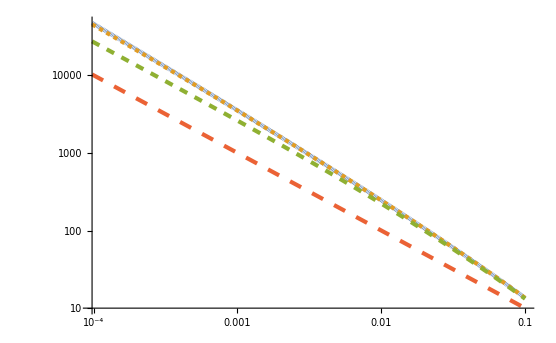

```mathematica
LogLogPlot[{Log[w110/w000]/Log[w111/w000]/.{p->0.001,q->2},Log[w110/w000]/Log[w111/w000]/.{p->0.01,q->2},Log[w110/w000]/Log[w111/w000]/.{p->0.1,q->2},1/Γ},{Γ,0,.1},
PlotStyle->dashThick,
PlotLegends->LineLegend[Automatic,{0.001,0.01,0.1,MaTeX["\\frac{1}{\\Gamma}"]},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2.5]],
AxesLabel->{MaTeX["\\Gamma",Magnification->2.5],MaTeX["\\Gamma \cdot t_{AB}^*(p,\\Gamma)",Magnification->2.5]},LabelStyle->{FontSize->16},ImageSize->300]
```

```mathematica
-Log[w111/w000]
```

-Log[(-((1-2 p+2 p^2)^2 (q+2 Γ^2)^2)/(q^2 (-1+q^4))+((p^2 (1+(-1+q) ((1-Γ)^2+Γ^2))+(1-p)^2 (1+2 (-1+q) (1-Γ)+(-2+q) (-1+q) (1-Γ)^2+(-1+q) ((1-Γ)^2+Γ^2)))^2)/(-1+q^4))/(((q^2-2 p q^2+2 p^2 (1/2 q (1+q)+Γ^2))^2)/(-1+q^4)-((q-2 p q+p^2 (2 q-2 (-1+q) (Γ-Γ^2)))^2)/(q^2 (-1+q^4)))]

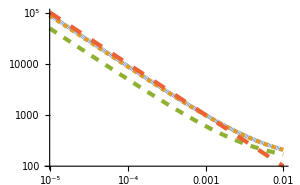

/Users/cathy/Google Drive/Random circuits/Pics/S_ABsatTime.png

```mathematica
n=250;
SABsatTime2 = LogLogPlot[{(-(n-2)^2/2 Log[w111]+n^2/2*Log[w000]-(2n-4)*Log[w100]-2Log[w110] )/(n * (-Log[w111/w000]))/.{p->0.01,q->2},(-(n-2)^2/2 Log[w111]+n^2/2*Log[w000]-(2n-4)*Log[w100]-2Log[w110] )/(n * (-Log[w111/w000]))/.{p->0.1,q->2},
(-(n-2)^2/2 Log[w111]+n^2/2*Log[w000]-(2n-4)*Log[w100]-2Log[w110] )/(n * (-Log[w111/w000]))/.{p->0.5,q->2},1/Γ},
{Γ,0,.01},
PlotStyle->dashThick,
Ticks->{{10^-5,10^-4,10^-3,10^-2},{10^3,10^4,10^5}},
PlotLegends->LineLegend[Automatic,{0.01,0.1,0.5,MaTeX["\\frac{1}{\\Gamma}"]},Spacings->0.15,LegendLabel->MaTeX["p",Magnification->2]],
AxesLabel->{MaTeX["\\Gamma",Magnification->2],MaTeX["t_{AB}^*(p,\\Gamma)",Magnification->2]},LabelStyle->{FontSize->16},ImageSize->300]
Export["/Users/cathy/Google Drive/Random circuits/Pics/S_ABsatTime.png",Rasterize[SABsatTime2,ImageResolution->150]]
```

```mathematica
plots2=GraphicsRow[{SABsatTime,SABsatTime2},Spacings->-1,ImageSize->{750,230}]
```

-Graphics-

/Users/cathy/Google Drive/Random circuits/Pics/S_ABsatTime.png

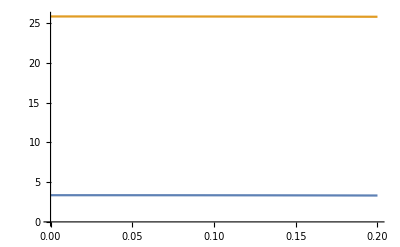

```mathematica
SABsatTime = Plot[{(-(2n-4)Log[w100/w000]-n(n-1)/4*Log[w111/w000])/(-n*Log[w111/w000])*Γ/.{Γ->0.001,q->2},(-(2n-4)Log[w100/w000]-n(n-1)/4*Log[w111/w000])/(-n*Log[w111/w000])*Γ/.{Γ->0.01,q->2}},{p,0,0.2},PlotLegends->LineLegend[Automatic,{0.001,0.01},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2]],
AxesLabel->{MaTeX["p",Magnification->2],MaTeX["\\Gamma \cdot t_{AB}^*(p,\\Gamma)",Magnification->2]},LabelStyle->{FontSize->22}]
```

```mathematica
n=10;
1/n*(-n Log[w101]-n ^2/2 Log[w111] )/(n/2 * (-Log[w111])+2*(-Log[w101]-Log[2]))/.{Γ->0.0001,q->2,p->0.0}
```

2.04971

```mathematica
w111/.{Γ->0.0001,q->2,p->0.0}
```

0.999787

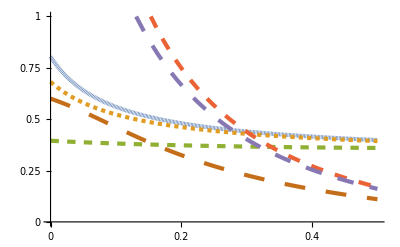

```mathematica
n=300;
dashThick=Transpose[{Table[AbsoluteDashing[i],{i,0,17,3}],
Table[AbsoluteThickness[3],{i,1,6}]}];
SAsatTime = Plot[{1/n*(-n Log[w101]-n(n-1)/8 Log[w111/w000] )/(n/2 * (-Log[w111/w000])-Log[w111]+(-Log[w101*w100]-Log[2]))/.{Γ->0.,q->2},1/n*(-n Log[w101]-n(n-1)/8 Log[w111/w000] )/(n/2 * (-Log[w111/w000])-Log[w111]+(-Log[w101*w100]-Log[2]))/.{Γ->0.001,q->2},1/n*(-n Log[w101]-n(n-1)/8 Log[w111/w000] )/(n/2 * (-Log[w111/w000])-Log[w111]+(-Log[w101*w100]-Log[2]))/.{Γ->0.01,q->2},1/n*(-n/2 Log[w110/w111] )/(n/2 * (-Log[w111/w000])+(-Log[w101*w100]-Log[2]))/.{Γ->0,q->2},1/n*(-n /2 Log[w110/w111] )/(n/2 * (-Log[w111/w000])+(-Log[w101*w100]-Log[2]))/.{Γ->0.001,q->2},1/n*(-n /2 Log[w110/w111] )/(n/2 * (-Log[w111/w000])+(-Log[w101*w100]-Log[2]))/.{Γ->0.01,q->2}},{p,0,0.5},
PlotStyle->dashThick,PlotLegends->LineLegend[Automatic,{"▼ 0","▼ 0.001","▼ 0.01","□ 0" ,"□ 0.001","□ 0.01"},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2]],
Ticks->{{0,0.1,0.2,0.3,0.4,0.5},{0,0.25,0.5,0.75,1}},
AxesLabel->{MaTeX["p",Magnification->2],MaTeX["t_A^*(p,\\Gamma)/N",Magnification->2]},LabelStyle->{FontSize->22},PlotRange->{{0,0.5},{0,1}}]
(*Export["/Users/cathy/Google Drive/Random circuits/Pics/S_AsatTime.png",Rasterize[SAsatTime,ImageResolution->150]]*)
```

30

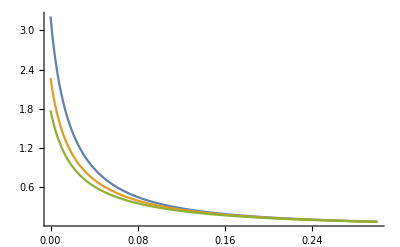

```mathematica
n=30
SAsatTime = Plot[{1/n*(-n/2 Log[w110/w111] )/(n/2 * (-Log[w111])+(-Log[w101*w100]-Log[2]))/.{Γ->0.001,q->2},1/n*(-n /2 Log[w110/w111] )/(n/2 * (-Log[w111])+(-Log[w101*w100]-Log[2]))/.{Γ->0.005,q->2},1/n*(-n /2 Log[w110/w111] )/(n/2 * (-Log[w111])+(-Log[w101*w100]-Log[2]))/.{Γ->0.01,q->2}},{p,0,0.3},PlotLegends->LineLegend[Automatic,{0,0.001,0.01,0.1},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2]],
AxesLabel->{MaTeX["p",Magnification->2],MaTeX["t^*(p,\\Gamma)/N",Magnification->2]},LabelStyle->{FontSize->22},PlotRange->Full]
```

```mathematica
{wmin[[2]]/.{Γ->0.001,q->2,n->1000000,p->0.1}}[[1]][[1]]
```

w→3.00877

```mathematica
FreeEnergy/.{{wmin[[2]]/.{Γ->0.001,q->2,n->1000000,p->0.1}}[[1]][[1]],Γ->0.001,q->2,n->1000000000}
```

-1.10153-3.00877×10^9 Log[1/15 (3.996 (1-p)^2+1.998 p^2)^2-0.0666668 (1-2 p+2 p^2)^2]-1.66181×10^8 Log[-1/60 (3.996 (1-p)^2+1.998 p^2)^2+0.266667 (1-2 p+2 p^2)^2]-1.66764×10^9 Log[-1/60 (3.996 (1-p)^2+1.998 p^2) (2-4 p+3.998 p^2)+0.133333 (1-2 p+2 p^2) (4-8 p+6. p^2)]-(-3.3382×10^9+1000000000 t) Log[-1/60 (2-4 p+3.998 p^2)^2+1/15 (4-8 p+6. p^2)^2]

```mathematica
Solve[D[FreeEnergy,{w,1}]==0,{w}]
```

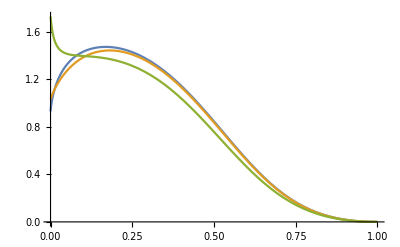

```mathematica
(*w=Sqrt[(Log[w110*w000])/(2*(Log[w111/w000]))];*)
Clear[w,n]
FreeEnergy=n w *(-Log[w111])-n/w(2w-1)Log[w100]-(n/(2w)-1)Log[w110]-(n t-(n w+n/(w)(2w-1)+(n/(2w)-1))+(n/2w-1))Log[w000]-Log[w];
wmin = Solve[D[FreeEnergy,{w,1}]==0,{w}];
tAB = Solve[FreeEnergy==-Log[w111]*n t,t];

tab = 1/(-Log[w111/w000])*(w*w111+(1-1/w)w100+(1/(2w)-1)Log[w110]+(w+2-1/(2w))Log[w000]-1/n Log[w]);
tAB = Plot[{Γ*t/.{{tAB/.{{wmin[[2]]/.{Γ->0.001,q->2,n->1000000}}[[1]][[1]],Γ->0.001,q->2,n->1000000000}}[[1]][[1]][[1]],Γ->0.001},Γ*t/.{{tAB/.{{wmin[[2]]/.{Γ->0.01,q->2,n->1000000}}[[1]][[1]],Γ->0.01,q->2,n->1000000000}}[[1]][[1]][[1]],Γ->0.01},Γ*t/.{{tAB/.{{wmin[[2]]/.{Γ->0.01,q->2,n->1000000}}[[1]][[1]],Γ->0.1,q->2,n->1000000000}}[[1]][[1]][[1]],Γ->0.1}},{p,0,1}]
```

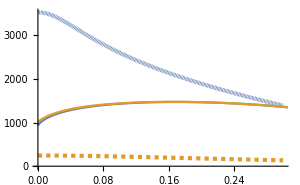

```mathematica
Show[SAsatTime,tAB]
```

```mathematica
w000/.{p->0,Γ->0.0,q->2}
```

1.

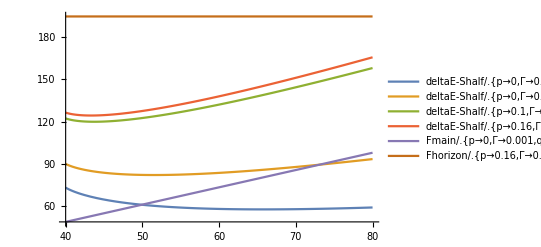

```mathematica
nTot=40;
deltaE =(h+nTot)*(-Log[w100])+(h-nTot)*(-Log[w101]) +h*nTot/2*(-Log[w111/w000]);
Shalf = Log[Sum[Binomial[h,y]*Binomial[h,(y-nTot)],{y,nTot,h}]];
deltaEtot = 2 (h+nTot)*(-Log[w100])+2(h-nTot)*(-Log[w101]) +h*nTot*(-Log[w111/w000]);
Stot =Log[nTot/2]+ 2Log[nTot  * Sum[Binomial[h,y]*Binomial[h,(y-nTot)],{y,nTot,h}]];
Fmain = h(-Log[w100*w101]-nTot*(Log[w111/w000])-Log[2]);
Fhorizon=-nTot*Log[w110];
Plot[{deltaE-Shalf/.{p->0,Γ->0.0,q->2},deltaE-Shalf/.{p->0,Γ->0.01,q->2},deltaE-Shalf/.{p->0.1,Γ->0.01,q->2},deltaE-Shalf/.{p->0.16,Γ->0.001,q->2},Fmain/.{p->0,Γ->0.001,q->2},Fhorizon/.{p->0.16,Γ->0.01,q->2}},{h,nTot,nTot*2},PlotLegends->"Expressions",AxesLabel->{MaTeX[h,Magnification->2],MaTeX[F,Magnification->2]}]
(*FindMinimum[deltaE+Shalf/.{p->0.1,Γ->0.01,q->2},{h,nTot/2}]*)
```

Null

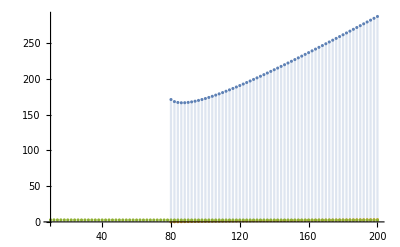

```mathematica
Null
```

```mathematica
Plot[Shalf/]
```

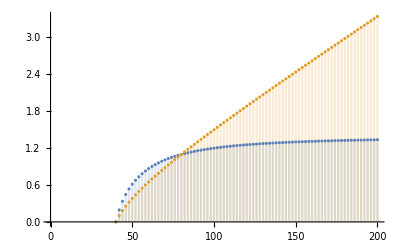

100

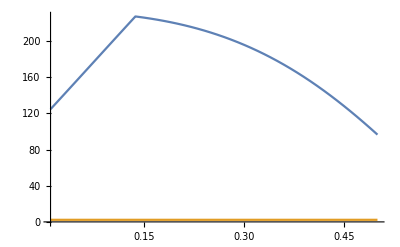

```mathematica
Clear[Γ,q]
n=100
Plot[{
Min[-n Log[w101*w010]-Log[Binomial[n,n/2]],-2n Log[w101*w010/w111/w000]-2Log[Binomial[n,n/2]]]/.{q->2,Γ->0.001}, 1/2 Log[n]},{p,0.01,0.5}, PlotLegends->LineLegend[Automatic,{0,0.001,0.01,0.05,0.1},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2]],AxesLabel->{MaTeX["p",Magnification->2],MaTeX["I(p,\\Gamma)/N",Magnification->2]},LabelStyle->{FontSize->22}]
```

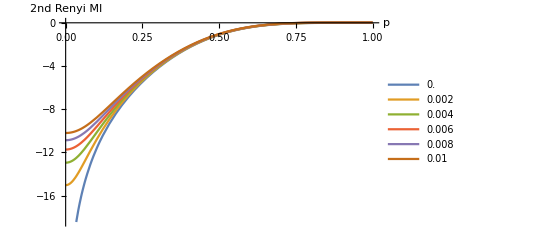

```mathematica
Plot[Evaluate@Table[(-3 Log[w010*w100/w110]-Log[w111]+4Log[w000])/.{q->2,Γ->.0001*g},{g,0,100,20}],{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.0001*g,{g,0,100,20}],Spacings->0.15]]
```

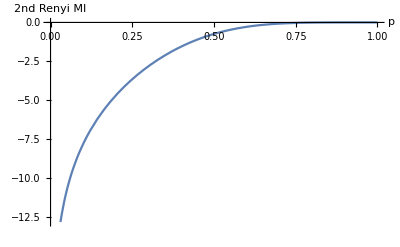

```mathematica
Plot[-2Log[w100*w010/(w110* w000)]/.{q->2,Γ->0},{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.0001*g,{g,0,100,20}],Spacings->0.15]]
```

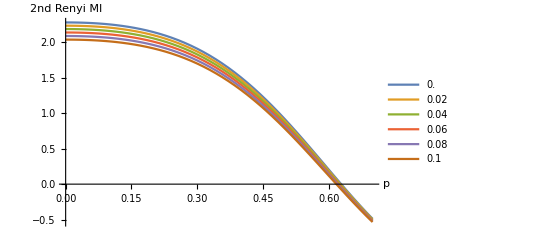

```mathematica
Plot[Evaluate@Table[-2Log[2w010*w101/(w111* w000)]/.{q->2,Γ->.01*g},{g,0,10,2}],{p,0,0.7},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.01*g,{g,0,10,2}],Spacings->0.15]]
```

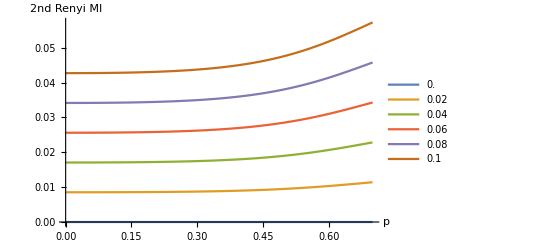

```mathematica
Plot[Evaluate@Table[2Log[w000/ w111]/.{q->2,Γ->.001*g},{g,0,10,2}],{p,0,0.7},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.01*g,{g,0,10,2}],Spacings->0.15]]
```

32

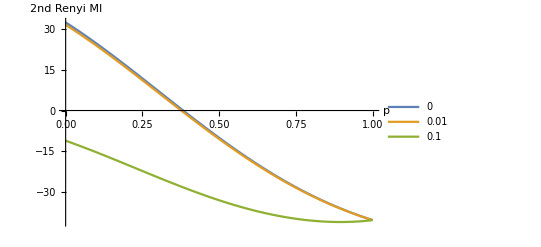

```mathematica
n=32
renyiVol = Plot[{-2n Log[2w100*w011/(w111*w000)]-2Log[Binomial[n,n/2]]/.{q->2,p->0},
-2n Log[2w100*w011/(w111*w000)]-2Log[Binomial[n,n/2]]/.{q->2,p->0.1},
-2n Log[2w100*w011/(w111*w000)]-2Log[Binomial[n,n/2]]/.{q->2,p->0.5}},{Γ,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->{0,0.01,0.1}]
```

Null

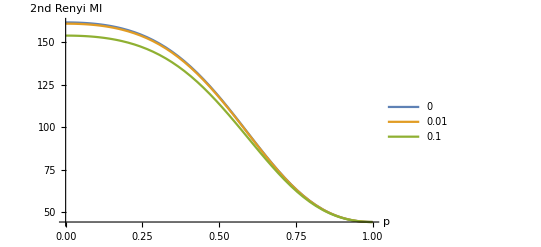

/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2_volume.png

```mathematica
n=32
renyiVol = Plot[{-2n Log[w100*w011/(2w111*w000) ]/.{q->2,Γ->0},
-2n Log[w100*w011/(2w111*w000)]/.{q->2,Γ->0.01},
-2n Log[w100*w011/(2w111*w000)]/.{q->2,Γ->0.1}},{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->{0,0.01,0.1}]
Export["/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2_volume.png",Rasterize[renyiVol,ImageResolution->150]]
```

```mathematica
W000[p_,q_,Γ_]:=w3test[1,1,1,q,Γ,p];
W001[p_,q_,Γ_]:=w3test[1,1,-1,q,Γ,p];
W010[p_,q_,Γ_]:=w3test[1,-1,1,q,Γ,p];
W100[p_,q_,Γ_]:=w3test[-1,1,1,q,Γ,p];
W101[p_,q_,Γ_]:=w3test[-1,1,-1,q,Γ,p];
W011[p_,q_,Γ_]:=w3test[1,-1,-1,q,Γ,p];
W110[p_,q_,Γ_]:=w3test[-1,-1,1,q,Γ,p];
W111[p_,q_,Γ_]:=w3test[-1,-1,-1,q,Γ,p];
```

## The mixed boundary condition

```mathematica
FHalfUpDown[n_]:=-(n-1)(Log[w010*w011]-(n/2-1)(n-1)Log[(w000*w111)]-n Log[2])
FHalfMostUp[n_]:=(-(7/8n^2-7n/4)Log[w000]-(n^2/8-n/4)Log[w111]-n Log[w101])
FHalfMostDown[n_]:=(-(7/8n^2-7n/4)Log[w111]-(n^2/8-n/4)Log[w000]-n Log[ w100])
FHalfUpHDomWall[n_]:=(-(n(n-1)-n/2-1)Log[w000]-(n/2-1)Log[w110]-Log[w010]-Log[w100])
FHalfDownHDomWall[n_]:=(-(n(n-1)-n/2-1)Log[w111]-(n/2-1)Log[w001]-Log[w101]-Log[w011])
(*MinValue[{FHalfUpDown[n]/.{q->2,Γ->0.01}||FHalfMostUp[n]/.{q->2,Γ->0.01}||FHalfMostDown[n]/.{q->2,Γ->0.01},p>0},p]*)
FHalf1[n_,p_,q_,Γ_]:=(-(n/2-1)(n-1)Log[(W000[p,q,Γ]*W111[p,q,Γ])]-(n-1)(Log[W010[p,q,Γ]*W011[p,q,Γ]]))-n Log[2]
FHalf2[n_,p_,q_,Γ_]:=(-(7/8n^2-7n/4)Log[W000[p,q,Γ]]-(n^2/8-n/4)Log[W111[p,q,Γ]]-n Log[W101[p,q,Γ]])
FHalf3[n_,p_,q_,Γ_]:=(-(7/8n^2-7n/4)Log[W111[p,q,Γ]]-(n^2/8-n/4)Log[W000[p,q,Γ]]-n Log[ W100[p,q,Γ]])
FHalf4[n_,p_,q_,Γ_]:=(-(n(n-1)-n/2-1)Log[W000[p,q,Γ]]-(n/2-1)Log[W110[p,q,Γ]]-Log[W010[p,q,Γ]]-Log[W100[p,q,Γ]])
FHalf5[n_,p_,q_,Γ_]:=(-(n(n-1)-n/2-1)Log[W111[p,q,Γ]]-(n/2-1)Log[W001[p,q,Γ]]-Log[W101[p,q,Γ]]-Log[W011[p,q,Γ]])
FABMin [n_,p_,q_,Γ_]:= Min[FHalf1[n,p,q,Γ],FHalf2[n,p,q,Γ], FHalf3[n,p,q,Γ],FHalf4[n,p,q,Γ],FHalf5[n,p,q,Γ]]
```

## Null

```mathematica
Null
```

## Null

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

30

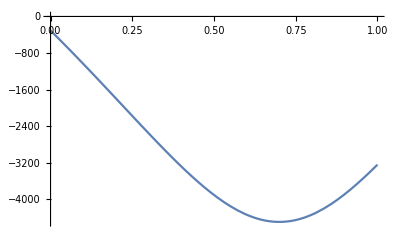

```mathematica
minMutual [n_,p_,q_,Γ_]:= Min[FHalf4[n,p,q,Γ]+FHalf5[n,p,q,Γ]-FDownAll[n,p,q,Γ]-FUpAll[n,p,q,Γ],2FHalf1[n,p,q,Γ]-FUpAll[n,p,q,Γ]-FDownAll[n,p,q,Γ],2FHalf1[n,p,q,Γ]-FDownMostDown[n,p,q,Γ]-FUpMostUp[n,p,q,Γ],2FHalf1[n,p,q,Γ]-FUpAll [n,p,q,Γ]-FUpMostUp[n,p,q,Γ],FHalf2[n,p,q,Γ]-FHalf3[n,p,q,Γ]-FUpAll[n,p,q,Γ]-FDownAll[n,p,q,Γ]
]
n=30
q=2;
Clear[Γ,q]
Plot[minMutual[n,p,q,Γ]/.{n->10,q->2,Γ->0.1},{p,0,1}]
```

30

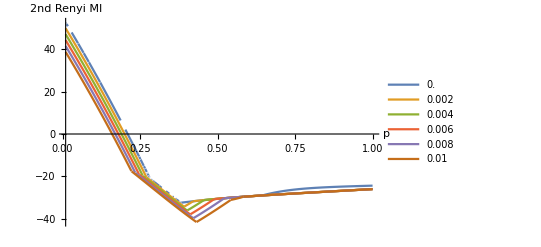

```mathematica
n=30
q=2;
Plot[Evaluate[Table[(2 FABMin [n,p,q,g*0.001]-FDownMin[n,p,q,g*0.001]-FUpMin[n,p,q,g*0.001]),{g,0,10,2}]],{p,0.01,1},AxesLabel->{"p","2nd Renyi MI"},PlotLegends->LineLegend[Automatic,Table[g*0.001,{g,0,10,2}]],LabelStyle->{FontSize->22}]
```

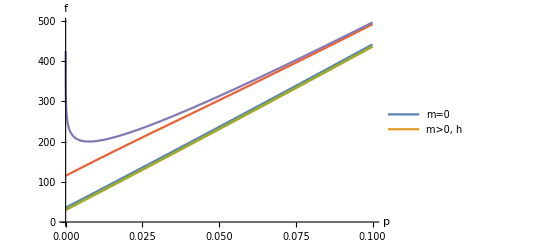

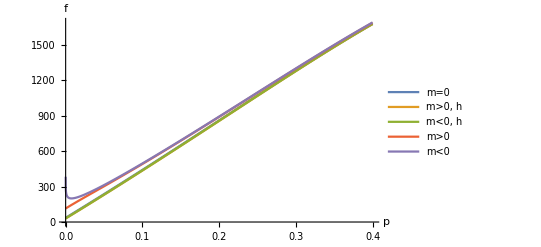

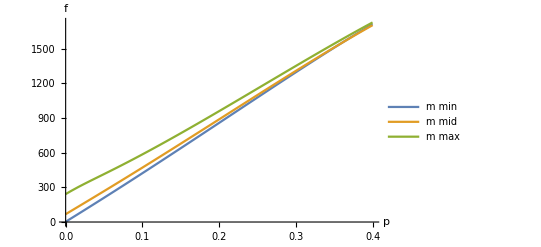

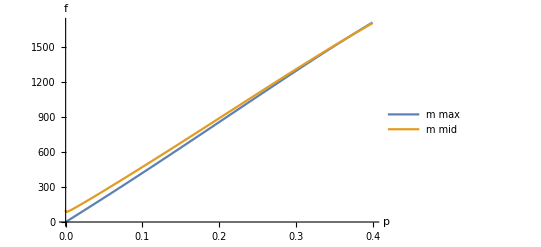

```mathematica
n=32;
q=2;
Γ=0.001;
Plot[Evaluate[{FHalf1[n,p,q,Γ],FHalf2[n,p,q,Γ],FHalf3[n,p,q,Γ],FHalf4[n,p,q,Γ],FHalf5[n,p,q,Γ]}],{p,0,0.1},AxesLabel->{"p","f"},PlotLegends->{"m=0","m>0, h"},LabelStyle->{FontSize->22}]
Plot[Evaluate[{FHalf1[n,p,q,Γ],FHalf2[n,p,q,Γ],FHalf3[n,p,q,Γ],FHalf4[n,p,q,Γ],FHalf5[n,p,q,Γ]}],{p,0,0.4},AxesLabel->{"p","f"},PlotLegends->{"m=0","m>0, h","m<0, h","m>0","m<0"},LabelStyle->{FontSize->22}]
Plot[Evaluate[{FDownAll[n,p,q,Γ],FDownMostDown[n,p,q,Γ],FDownH[n,p,q,Γ]}],{p,0,0.4},AxesLabel->{"p","f"},PlotLegends->{"m min","m mid","m max"},LabelStyle->{FontSize->22}]
Plot[Evaluate[{FUpAll[n,p,q,Γ],FUpMostUp[n,p,q,Γ]}],{p,0,0.4},AxesLabel->{"p","f"},PlotLegends->{"m max","m mid","m min"},LabelStyle->{FontSize->22}]
```

```mathematica
FAhalf1[n_]:=(2((n^2/2-n)(-Log[w000]-Log[w111])+n(-Log[w010]+-Log[w011]))-2n Log[2]-(-n(n-1)/2 Log[w111]-(n-1)(n-2)/2Log[ w001]-2(n-1)Log[w010]-Log[w001]-n Log[2] )-n^2Log[w000])/n^2
FAhalf1[n_]:=(2((n^2/2-n)(-Log[w000]-Log[w111])+n(-Log[w010]+-Log[w011]))-2n Log[2]-(-n(n-1)/2 Log[w111]-(n-1)(n-2)/2Log[ w001]-2(n-1)Log[w010]-Log[w001]-n Log[2] )-n^2Log[w000])/n^2

FAhalf[n_]:=MinValue[a x^2+b x+c,x]

FAm1[n_]:=(2(-(n^2/8-n/4)Log[w111]-n/2Log[ w100]-(7/8n^2-3n/4)Log[w000])+(n(n-1)/2Log[w111]+(n-1)(n-2)/2Log[ w000]+2(n-1)Log[w011]+Log[w001]+n Log[2]))/n^2
FAmm1[n_]:=(2(-(n^2/8-n/4)Log[w000]-n/2Log[ w101]-(7/8n^2-3n/4)Log[w111])+(n(n-1)/2Log[w111]+(n-1)(n-2)/2 Log[w000]+2(n-1)Log[w011]+Log[w001]+n Log[2]))/n^2
```

30

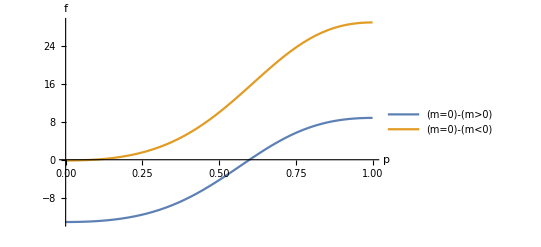

```mathematica
n=30
Plot[Evaluate[{-FHalfUpDown[n] + FHalfMostUp[n],-FHalfUpDown[n] + FHalfMostDown[n]}/.{q->2,Γ->0.01}],{p,0,1},AxesLabel->{"p","f"},PlotLegends->{"(m=0)-(m>0)","(m=0)-(m<0)"},LabelStyle->{FontSize->22}]
```

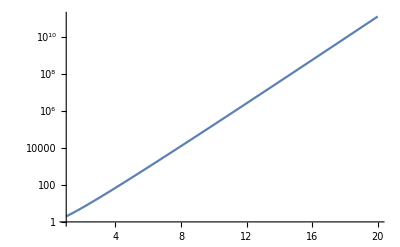

```mathematica
LogPlot[Binomial[2n,n],{n,1,20}]
```

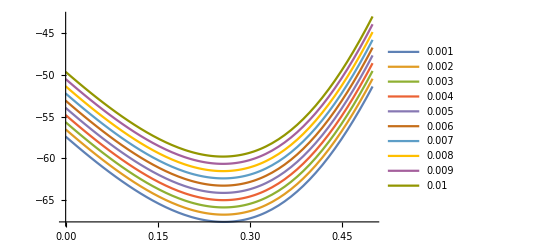

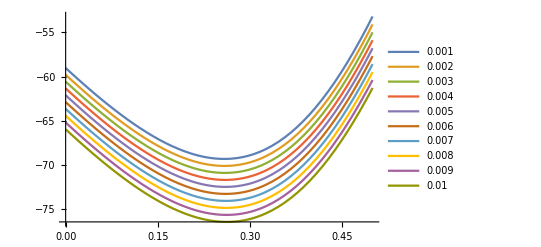

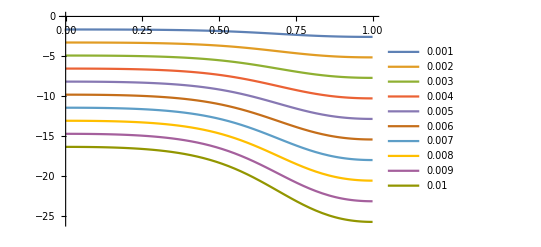

```mathematica
n=32;
Plot[Evaluate[Table[{Fbcmm1[n]-FbcHalf[n]}/.{q->2,Γ->0.001*g},{g,1,10}]],{p,0,0.5},PlotLegends->Table[0.001*g,{g,1,10}]]
Plot[Evaluate[Table[{Fbcm1[n]-FbcHalf[n]}/.{q->2,Γ->0.001*g},{g,1,10}]],{p,0,0.5},PlotLegends->Table[0.001*g,{g,1,10}]]
Plot[Evaluate[Table[{Fbcm1[n]-Fbcmm1[n]}/.{q->2,Γ->0.001*g},{g,1,10}]],{p,0,1},PlotLegends->Table[0.001*g,{g,1,10}]]
```

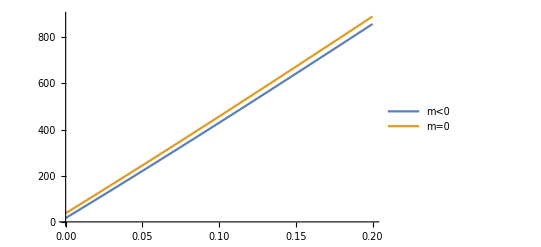

```mathematica
Plot[Evaluate[{Fbcmm1[n],FbcHalf[n]}/.{q->2,Γ->0.001}],{p,0,.2},PlotLegends->{"m<0","m=0","m>>0","m>0"}]
```

```mathematica
w000b/.{q->2,Γ->0,p->0}
```

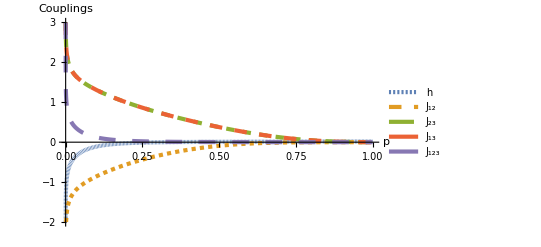

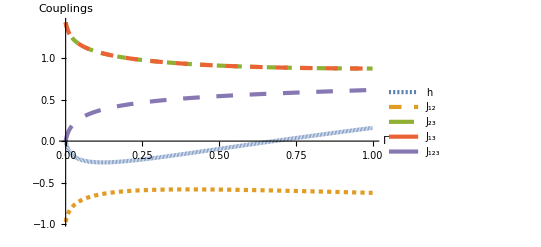

```mathematica
w000b=w3aExp[1,1,1,2,Γ,p];
w001b=w3aExp[1,1,-1,2,Γ,p];
w010b=w3aExp[1,-1,1,2,Γ,p];
w100b=w3aExp[-1,1,1,2,Γ,p];
w101b=w3aExp[-1,1,-1,2,Γ,p];
w011b=w3aExp[1,-1,-1,2,Γ,p];
w110b=w3aExp[-1,-1,1,2,Γ,p];
w111b=w3aExp[-1,-1,-1,2,Γ,p];
Mb={{1,1,1,1,1,1,1,1},
{1,1,1,-1,1,-1,-1,-1},
{1,1,-1,1,-1,-1,1,-1},
{1,-1,1,1,-1,1,-1,-1},
{1,-1,1,-1,-1,-1,1,1},
{1,1,-1,-1,-1,1,-1,1},
{1,-1,-1,1,1,-1,-1,1},
{1,-1,-1,-1,1,1,1,-1}};
MbI = Inverse[Mb];
vb= MbI.Log[{w000b,w001b,w010b,w100b,w101b,w011b,w110b,w111b}];
vLegend={"h0","h1","h2","h3","J12","J23","J31","J123"};
vNewb = {vb[[2]]+vb[[3]]+vb[[4]],vb[[5]],vb[[6]],vb[[7]],vb[[8]]};
vNewLegend={"h", "J_12", "J_23", "J_13", "J_123"};
dashThick=Transpose[{Table[AbsoluteDashing[i],{i,0,14,3}],
Table[AbsoluteThickness[3],{i,1,5}]}];
Plot[Evaluate @Table[Indexed[vNewb/.{q->2,Γ->0.01},i],{i,5}],{p,0,1},PlotLegends->LineLegend[Automatic,vNewLegend,Spacings->0.15],AxesLabel->{"p","Couplings"},LabelStyle->{FontSize->22},PlotStyle->dashThick, PlotRange-> {{0,1},{-2,3}}]
Plot[Evaluate @Table[Indexed[vNewb/.{q->2,p->0.1},i],{i,5}],{Γ,0,1},PlotLegends->LineLegend[Automatic,vNewLegend,Spacings->0.15],AxesLabel->{"Γ","Couplings"},LabelStyle->{FontSize->22},PlotStyle->dashThick, PlotRange-> Automatic]
```

```mathematica
w000=w3test[1,1,1,q,Γ,p];
w001=w3test[1,1,-1,q,Γ,p];
w010=w3test[1,-1,1,q,Γ,p];
w100=w3test[-1,1,1,q,Γ,p];
w101=w3test[-1,1,-1,q,Γ,p];
w011=w3test[1,-1,-1,q,Γ,p];
w110=w3test[-1,-1,1,q,Γ,p];
w111=w3test[-1,-1,-1,q,Γ,p];

M={{1,1,1,1,1,1,1,1},{1,1,1,-1,1,-1,-1,-1},{1,1,-1,1,-1,-1,1,-1},{1,-1,1,1,-1,1,-1,-1},{1,1,-1,-1,-1,1,-1,1},{1,-1,1,-1,-1,-1,1,1},{1,-1,-1,1,1,-1,-1,1},{1,-1,-1,-1,1,1,1,-1}};
MI = Inverse[M];
v= MI.Log[{w000,w001,w010,w100,w101,w011,w110,w111}];
vLegend={"h0","h1","h2","h3","J12","J23","J31","J123"};
```

```mathematica
-Log[{w000,w001,w010,w100,w101,w011,w110,w111}]/.{p->0.1,q->2,Γ->0.001}
```

(0.409955
6.12843
1.31898
1.31898
1.32063
1.32063
5.97885
0.412077)

```mathematica
Collect[Series[v[[6]]/.q->2,{Γ,0,2},{p,0.16,2}],p]/.Γ->0 
Collect[Series[v[[5]]/.q->2,{Γ,0,2},{p,0.16,2}],p]/.Γ->0 
Collect[Series[v[[8]]/.q->2,{Γ,0,2},{p,0.16,2}],p]
Collect[Series[(v[[1]]+v[[2]]+v[[3]])/.q->2,{
Γ,0,2},{p,0.16,2}],p]/.Γ->0
```

1.99661-6.74717 p+9.5378 p^2

-1.54216+6.81362 p-10.2006 p^2

49.2581 Γ-3638.4 Γ^2+p^2 (1022.67 Γ-98924.6 Γ^2)+p (-429.721 Γ+37359.6 Γ^2)

-2.44423+2.56421 p-9.34545 p^2

```mathematica
Perhaps one needs to reverse this using the Virial expansion, i.e. writing p,Gamma in terms of J12, J23, J123 etc at different orders of p and Gamma.
```

```mathematica
Simplify[wdtest[1,1,q,0,p]-wdtest[-1,-1,q,0,p]]
Simplify[wdtest[1,-1,q,0,p]-wdtest[-1,1,q,0,p]]
Simplify[w3test[1,1,1,2,0,p]-w3test[-1,-1,-1,2,0,p]]
```

0

0

0

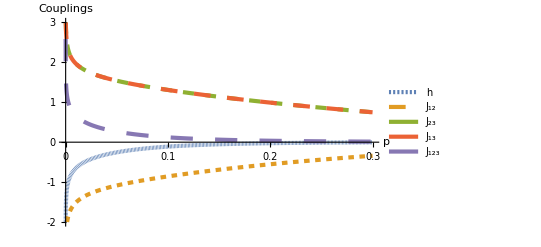

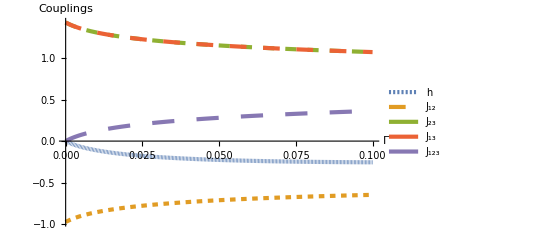

```mathematica
vNewb = {v[[2]]+v[[3]]+v[[4]],v[[5]],v[[6]],v[[7]],v[[8]]};
vNewLegend={"h", "J_12", "J_23", "J_13", "J_123"};
dashThick=Transpose[{Table[AbsoluteDashing[i],{i,0,16,4}],
Table[AbsoluteThickness[3],{i,1,5}]}];
phaseDampGamma001q2 = Plot[Evaluate @Table[Indexed[vNew/.{q->2,Γ->0.01},i],{i,5}],{p,0,0.3},PlotLegends->LineLegend[Automatic,vNewLegend,Spacings->0.15],AxesLabel->{"p","Couplings"},LabelStyle->{FontSize->22},PlotStyle->dashThick, PlotRange-> {{0,0.3},{-2,3}},Ticks-> {{0,0.1,0.2,0.3},{-2,-1,0,1,2,3}}]
Export["/Users/cathy/Google Drive/Random circuits/Pics/ampDamp_Gammma001_q2.png",Rasterize[phaseDampGamma001q2,ImageResolution->150]];
phaseDampp01q2 = Plot[Evaluate @Table[Indexed[vNew/.{q->2,p->0.1},i],{i,5}],{Γ,0,0.1},PlotLegends->LineLegend[Automatic,vNewLegend,Spacings->0.15],AxesLabel->{"Γ","Couplings"},LabelStyle->{FontSize->22},PlotStyle->dashThick, PlotRange-> Automatic]
Export["/Users/cathy/Google Drive/Random circuits/Pics/ampDamp_p01_q2.png",Rasterize[phaseDampp01q2,ImageResolution->150]];
```

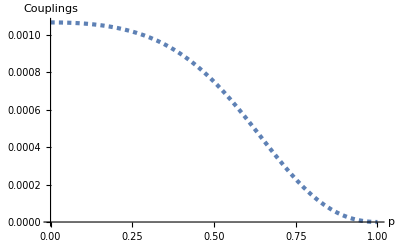

```mathematica
Plot[ vNew[[5]]+ vNew[[1]]/.{q->2,Γ->0.001},{p,0,1},AxesLabel->{"p","Couplings"},LabelStyle->{FontSize->22},PlotStyle->dashThick]
```

(2^-n √π Binomial[n,n/2] Gamma[1+2 n])/(Gamma[(1+n)/2] Gamma[1/2 (2+3 n)])

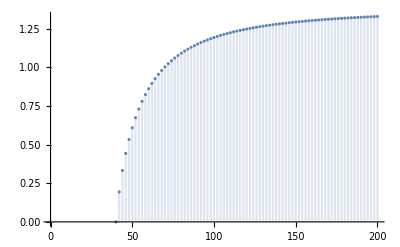

```mathematica
Clear[n]
Sum[Binomial[n,y]*Binomial[n,n/2-y],{y,0,n}]
```

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

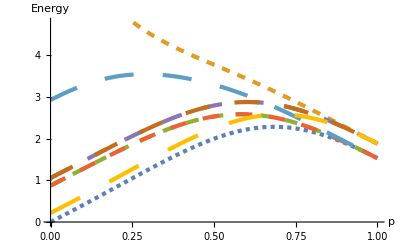

/Users/cathy/Google Drive/Random circuits/Pics/w3_math.png

```mathematica
dashThick=Transpose[{Table[AbsoluteDashing[i],{i,3,25,3}],
Table[AbsoluteThickness[3],{i,1,8}]}];
wLegend=MaTeX[{"w^{(2)}(\\uparrow \\uparrow \\uparrow)","w^{(2)}(\\uparrow \\uparrow \\downarrow)","w^{(2)}(\\uparrow \\downarrow \\uparrow)","w^{(2)}(\\downarrow \\uparrow \\uparrow)","w^{(2)}(\\downarrow \\uparrow \\downarrow)","w^{(2)}(\\uparrow \\downarrow \\downarrow)","w^{(2)}(\\downarrow \\downarrow \\uparrow)","w^{(2)}(\\downarrow \\downarrow \\downarrow)"},Magnification->1.5];
boltzmann3 =Plot[Evaluate[-Log[{w000,w001,w010,w100,w101,w011,w110,w111}]/.{q->2,Γ->0.1}],{p,0,1},PlotLegends->LineLegend[Automatic,wLegend,Spacings->0.15],AxesLabel->{"p","Energy"},LabelStyle->{FontSize->22},PlotRange->Automatic, PlotStyle->dashThick]
Export["/Users/cathy/Google Drive/Random circuits/Pics/w3_math.png",Rasterize[boltzmann3,ImageResolution->150]]
```

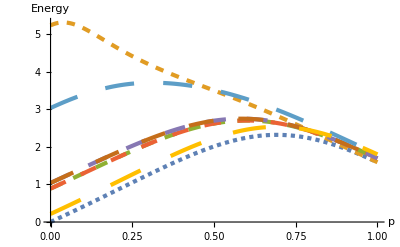

```mathematica
boltzmann3 =Plot[Evaluate[-Log[{w000b,w001b,w010b,w100b,w101b,w011b,w110b,w111b}]/.{q->2,Γ->0.1}],{p,0,1},PlotLegends->LineLegend[Automatic,wLegend,Spacings->0.15],AxesLabel->{"p","Energy"},LabelStyle->{FontSize->22},PlotRange->Automatic, PlotStyle->dashThick]
```

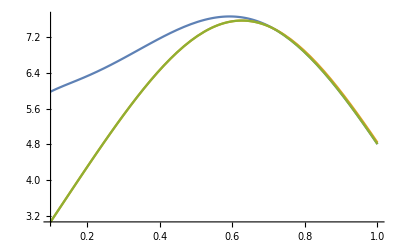

```mathematica
Plot[Evaluate[{-Log[w110*w000^2],-Log[w111*w010*w100],-Log[max3Plaqs]}/.{q->2,Γ->0.01}],{p,0.1,1}]
```

```mathematica
FortranForm[ (v[[2]]+v[[3]]+v[[4]])/.{Γ->g}]
```

-Log(-((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -            (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -               (1 - g)**2*(-2 + q)*(-1 + q)))**2/(q**2*(-1 + q**4))) + 
     -      ((1 - 2*p + 2*p**2)**2*(2*g**2 + q)**2)/(-1 + q**4))/8. - 
     -  (3*Log((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -           (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -              (1 - g)**2*(-2 + q)*(-1 + q)))**2/(-1 + q**4) - 
     -       ((1 - 2*p + 2*p**2)**2*(2*g**2 + q)**2)/(q**2*(-1 + q**4))))/8. + 
     -  Log(-(((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -            (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -               (1 - g)**2*(-2 + q)*(-1 + q)))*(q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q)))/
     -        (q**2*(-1 + q**4))) + ((1 - 2*p + 2*p**2)*(2*g**2 + q)*
     -        (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.)))/(-1 + q**4))/4. - 
     -  Log(((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -          (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -             (1 - g)**2*(-2 + q)*(-1 + q)))*(q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q)))/
     -      (-1 + q**4) - ((1 - 2*p + 2*p**2)*(2*g**2 + q)*
     -        (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.)))/(q**2*(-1 + q**4)))/4. + 
     -  (3*Log(-((q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q))**2/(q**2*(-1 + q**4))) + 
     -       (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.))**2/(-1 + q**4)))/8. + 
     -  Log((q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q))**2/(-1 + q**4) - 
     -     (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.))**2/(q**2*(-1 + q**4)))/8.

```mathematica
FortranForm[v[[5]]/.{Γ->g}]
```

Log(-((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -           (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -              (1 - g)**2*(-2 + q)*(-1 + q)))**2/(q**2*(-1 + q**4))) + 
     -     ((1 - 2*p + 2*p**2)**2*(2*g**2 + q)**2)/(-1 + q**4))/8. + 
     -  Log((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -         (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -            (1 - g)**2*(-2 + q)*(-1 + q)))**2/(-1 + q**4) - 
     -     ((1 - 2*p + 2*p**2)**2*(2*g**2 + q)**2)/(q**2*(-1 + q**4)))/8. - 
     -  Log(-(((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -            (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -               (1 - g)**2*(-2 + q)*(-1 + q)))*(q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q)))/
     -        (q**2*(-1 + q**4))) + ((1 - 2*p + 2*p**2)*(2*g**2 + q)*
     -        (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.)))/(-1 + q**4))/4. - 
     -  Log(((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -          (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -             (1 - g)**2*(-2 + q)*(-1 + q)))*(q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q)))/
     -      (-1 + q**4) - ((1 - 2*p + 2*p**2)*(2*g**2 + q)*
     -        (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.)))/(q**2*(-1 + q**4)))/4. + 
     -  Log(-((q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q))**2/(q**2*(-1 + q**4))) + 
     -     (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.))**2/(-1 + q**4))/8. + 
     -  Log((q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q))**2/(-1 + q**4) - 
     -     (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.))**2/(q**2*(-1 + q**4)))/8.

```mathematica
FortranForm[v[[8]]/.{Γ->g}]
```

-Log(-((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -            (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -               (1 - g)**2*(-2 + q)*(-1 + q)))**2/(q**2*(-1 + q**4))) + 
     -      ((1 - 2*p + 2*p**2)**2*(2*g**2 + q)**2)/(-1 + q**4))/8. + 
     -  Log((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -         (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -            (1 - g)**2*(-2 + q)*(-1 + q)))**2/(-1 + q**4) - 
     -     ((1 - 2*p + 2*p**2)**2*(2*g**2 + q)**2)/(q**2*(-1 + q**4)))/8. + 
     -  Log(-(((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -            (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -               (1 - g)**2*(-2 + q)*(-1 + q)))*(q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q)))/
     -        (q**2*(-1 + q**4))) + ((1 - 2*p + 2*p**2)*(2*g**2 + q)*
     -        (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.)))/(-1 + q**4))/4. - 
     -  Log(((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -          (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -             (1 - g)**2*(-2 + q)*(-1 + q)))*(q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q)))/
     -      (-1 + q**4) - ((1 - 2*p + 2*p**2)*(2*g**2 + q)*
     -        (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.)))/(q**2*(-1 + q**4)))/4. - 
     -  Log(-((q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q))**2/(q**2*(-1 + q**4))) + 
     -     (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.))**2/(-1 + q**4))/8. + 
     -  Log((q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q))**2/(-1 + q**4) - 
     -     (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.))**2/(q**2*(-1 + q**4)))/8.

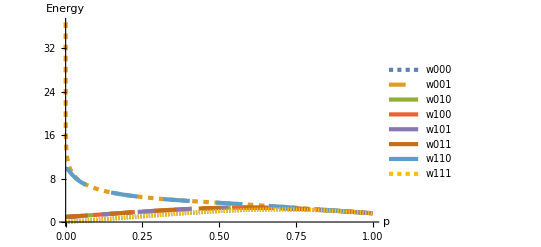

```mathematica
dashThick=Transpose[{Table[AbsoluteDashing[i],{i,1,19,3}],
Table[AbsoluteThickness[3],{i,1,7}]}];
BoltzmannW = {"w000","w001","w010","w100","w101","w011","w110","w111"};
p4=Plot[Evaluate @ Table[Indexed[-Log[{w000,w001,w010,w100,w101,w011,w110,w111}]/.{q->2,Γ->0.0001},i],{i,8}],{p,0,1},AxesLabel->{"p","Energy"},PlotLegends->LineLegend[Automatic,BoltzmannW,Spacings->0.15],LabelStyle->{FontSize->22},PlotStyle->dashThick,PlotRange->Full]
(*Export["/Users/cathy/Google Drive/Random circuits/Pics/phaseDamp_w3_Gamma01.png",Rasterize[p4,ImageResolution->150]]*)
```

```mathematica
Export["/Users/cathy/Google Drive/Random circuits/Pics/phaseDamp_Gamma001_q2.png",Rasterize[phaseDampGamma001q2,ImageResolution->150]];
```

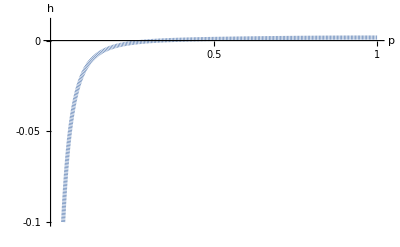

```mathematica
dashThick=Transpose[{Table[AbsoluteDashing[i],{i,0,16,4}],
Table[AbsoluteThickness[3],{i,1,5}]}];
exfield= Plot[Evaluate @ Table[Indexed[vNew/.{q->2,Γ->0.001},i],{i,1,1}],{p,0,1},AxesLabel->{Style["p",30],Style["h",30]},PlotStyle->{ColorData[97][1],dashThick[[1]]}, PlotRange-> {{0,1},{-0.1,0.01}},Ticks-> {{0.5,1},{0,-0.05,-0.1}},TicksStyle->{{20},{20}}]
```

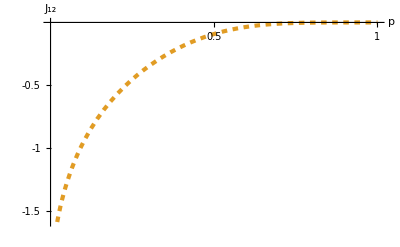

```mathematica
horJ= Plot[Evaluate @ Table[Indexed[vNew/.{q->2,Γ->0.001},i],{i,2,2}],{p,0,1},AxesLabel->{Style["p",30],Style["J_12",28]},PlotStyle->{ColorData[97][2],dashThick[[2]]},LabelStyle->{FontSize->22}, PlotRange-> Automatic,Ticks-> {{0.5,1},{-1.5,-1,-0.5}},TicksStyle->{{20},{20}}]
```

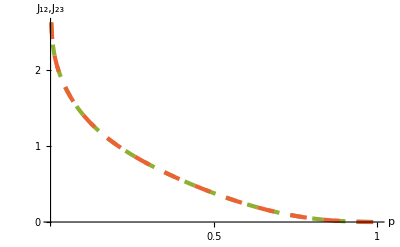

```mathematica
diaJ= Plot[Evaluate @ Table[Indexed[vNew/.{q->2,Γ->0.001},i],{i,3,4}],{p,0,1},AxesLabel->{Style["p",30],Style["J_12,J_23",28]},PlotStyle->{{ColorData[97][3],dashThick[[3]]},{ColorData[97][4],dashThick[[4]]}},LabelStyle->{FontSize->22}, PlotRange-> Automatic,Ticks-> {{0.5,1},{0,1,2}},TicksStyle->{{20},{20}}]
```

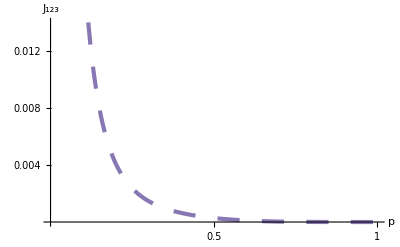

```mathematica
J123= Plot[Evaluate @ Table[Indexed[vNew/.{q->2,Γ->0.001},i],{i,5,5}],{p,0,1},AxesLabel->{Style["p",30],Style["J_123",28]},PlotStyle->{{ColorData[97][5],dashThick[[5]]}},LabelStyle->{FontSize->22}, PlotRange-> Automatic,Ticks-> {{0.5,1},{0.004,0.008,0.012}},TicksStyle->{{20},{20}}]
```

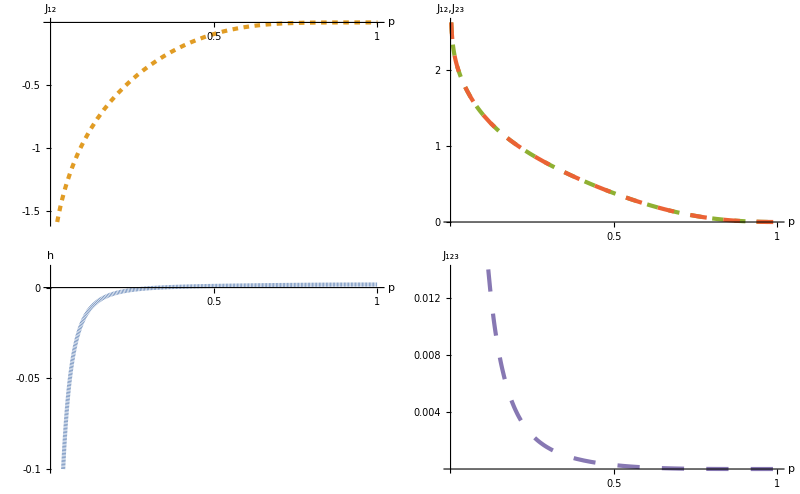

/Users/cathy/Google Drive/Random circuits/Pics/ampDamp_Gammma001_q2.png

```mathematica
phaseDampGamma001q2 = GraphicsGrid[{{horJ,diaJ},{exfield,J123}},Spacings->0]
Export["/Users/cathy/Google Drive/Random circuits/Pics/ampDamp_Gammma001_q2.png",Rasterize[phaseDampGamma001q2,ImageResolution->150]]
```